```mathematica
Calculation of the reflection coefficient for a simple ABC
Idea : Similar to dispersion relation caclulation 
1. Create ansatz with a reflected wave
2. Insert into discrete BC update schem
3. Calculate the amplitude of the reflected wave
4. Eliminate angular frequency using dispersion relation for waves
```

```mathematica
SetDirectory["/Users/kolesik/Ucenie/OPTI-547/pract/EP02-1D-Maxwell"]
```

/Users/kolesik/Ucenie/OPTI-547/pract/EP02-1D-Maxwell

```mathematica
eqn1 = -F[0,1] + F[1,0] + r ( F[1,1] - F[0,0])
```

-F[0,1]+F[1,0]+r (-F[0,0]+F[1,1])

```mathematica
Ansatz[x_,t_] := 1 Exp[-I k x -I om t] + R Exp[ +I k x - I om t]
```

```mathematica
eqn2 = eqn1/.F[a_,b_] -> Ansatz[a,b]
```

ⅇ^(-ⅈ k)-ⅇ^(-ⅈ om)+ⅇ^(ⅈ k) R-ⅇ^(-ⅈ om) R+r (-1+ⅇ^(-ⅈ k-ⅈ om)-R+ⅇ^(ⅈ k-ⅈ om) R)

```mathematica
solR = Simplify[Solve[eqn2==0,R][[1]]]
```

{R→(ⅇ^(-ⅈ k) (ⅇ^(ⅈ k)-ⅇ^(ⅈ om)-r+ⅇ^(ⅈ (k+om)) r))/(-1+ⅇ^(ⅈ (k+om))+ⅇ^(ⅈ k) r-ⅇ^(ⅈ om) r)}

```mathematica
aux1 = Simplify[ExpToTrig[R/.solR]]
```

((Cos[k]-ⅈ Sin[k]) (Sin[(k-om)/2]+r Sin[(k+om)/2]))/(r Sin[(k-om)/2]+Sin[(k+om)/2])

```mathematica
aux2 =TrigExpand[aux1];
```

```mathematica
This is where we use the dispersion relation to eliminate omega
```

```mathematica
aux3 = Simplify[(aux2/.Cos[om/2]->Sqrt[1-Sin[om/2]^2])/.Sin[om/2]-> dtoverdx Sin[k/2]]
```

((2 dtoverdx (-1+r) Cos[k/2]+(1+r) √(4-2 dtoverdx^2+2 dtoverdx^2 Cos[k])) (Cos[k]-ⅈ Sin[k]))/(-2 dtoverdx (-1+r) Cos[k/2]+(1+r) √(4-2 dtoverdx^2+2 dtoverdx^2 Cos[k]))

```mathematica
check0 =Simplify[Simplify[aux3/.k->0]/.r->(dtoverdx -1)/(dtoverdx +1)]
```

0

```mathematica
aux4 = Simplify[(aux3/.k-> 2 Pi/n)/.r->(dtoverdx -1)/(dtoverdx +1)]
```

((-2 Cos[π/n]+√(4-2 dtoverdx^2+2 dtoverdx^2 Cos[(2 π)/n])) (Cos[(2 π)/n]-ⅈ Sin[(2 π)/n]))/(2 Cos[π/n]+√(4-2 dtoverdx^2+2 dtoverdx^2 Cos[(2 π)/n]))

```mathematica
Log - scale reflection coefficient :
```

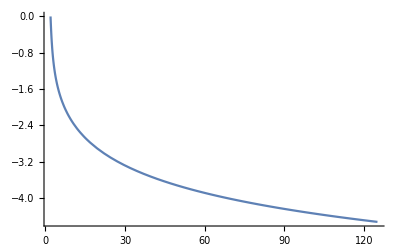

```mathematica
Plot[Log[10,Abs[aux4/.dtoverdx->0.9]],{n,2,125},PlotRange->All]
```